```mathematica
FindMinimum[] (* benutzt newton und co *)
NMinimize[] (* stochastische minimierung *)
```

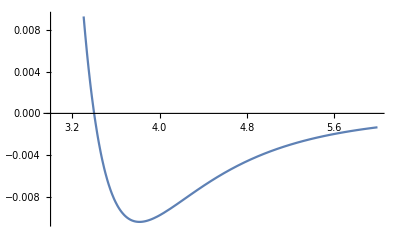

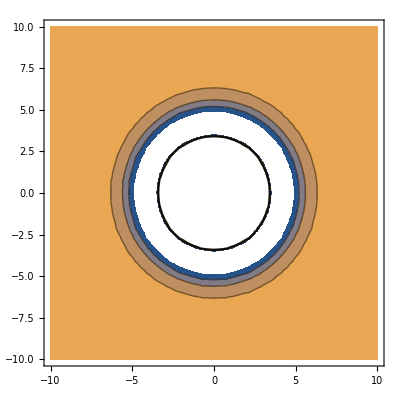

```mathematica
W[r_]=4 ϵ((σ/r)^12-(σ/r)^6);
Wv[x1_,x2_]:=W[EuclideanDistance[x1,x2]]
(* A point in space of molecule configurations is X={x1, y1, z1, x2, y2, z2, ...} *)
Ws[X_]:=Sum[Wv[X[[i]],X[[j]]],{i,1,Length[X]},{j,i+1,Length[X]}];

values = {ϵ -> 0.0104, σ->3.40};
ϵ=ϵ/.values;
σ = σ/.values;
Plot[W[r]/.values,{r,3,6}]
ContourPlot[Wv[{0,0,0},{x,y,0}],{x,-10,10},{y,-10,10}]
```

```mathematica
CaptainKirk[n_]:=(
Reap[Sow[{0.0,0.,0.}];
Sow[{x[2],0.,0.}];
Sow[{x[3],y[3],0}]
Do[Sow[{x[i],y[i],z[i]}],{i,4,n}]
][[2,1]]
)
```

```mathematica
Bones[n_]:=(
Reap[
Sow[{x[2],σ,.1 σ, 10σ}];
If[n>2,
Sow[{x[3],σ,.1 σ, 10σ}];
Sow[{y[3],σ,.1 σ, 10σ}];
];

If[n>3,
start={σ,σ,σ};
k=0;
Do[
Do[
Sow[{{x[i],y[i],z[i]}[[j]],start[[j]],.1σ,5 start[[j]]}];

k+=1;
,{j,{1,2,3}}];
start[[Mod[i-1,3]+1]]+=σ;
,{i,4,n}]

]
][[2,1]]
)
```

```mathematica
Engage[n_]:=(
sol[n]=FindMinimum[
Ws[CaptainKirk[n]],Bones[n]
 ][[2]];
Graphics3D[{PointSize[0.1],Point[CaptainKirk[n]/.sol[n]]},PlotRange->All]
)
```

```mathematica
Engage[9]
```

-Graphics3D-

```mathematica
Import["/home/eduard/enterp3.3ds"]
```